{Root1.00Root[-1000000000000000+1000000000000000 #1+#1^5&,1]0.999999999999999,Root-3.98 × 10^3-3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,2]-3976.603624187857,Root-3.98 × 10^3+3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,3]-3976.603624187857,Root3.98 × 10^3-3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,4]3976.103624187857,Root3.98 × 10^3+3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,5]3976.103624187857}

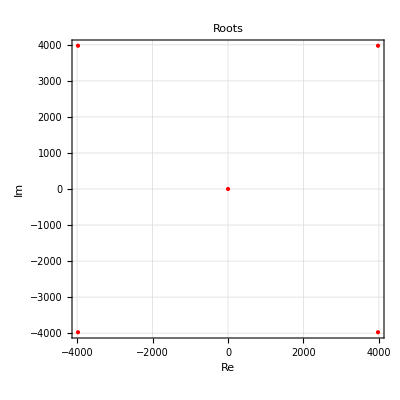

{200000000000000/(200000000000000+(Root1.00Root[-1000000000000000+1000000000000000 #1+#1^5&,1]0.999999999999999)^4),200000000000000/(200000000000000+(Root-3.98 × 10^3-3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,2]-3976.603624187857)^4),200000000000000/(200000000000000+(Root-3.98 × 10^3+3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,3]-3976.603624187857)^4),200000000000000/(200000000000000+(Root3.98 × 10^3-3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,4]3976.103624187857)^4),200000000000000/(200000000000000+(Root3.98 × 10^3+3.98 × 10^3 ⅈRoot[-1000000000000000+1000000000000000 #1+#1^5&,5]3976.103624187857)^4)}

```mathematica
a = 10^(-15);
b = 0;
g =1;
poly=a x^5 + b x^3 + g x - 1;
f = 1/poly;
roots=x/. Solve[poly==0,x]


ListPlot[{Re[#],Im[#]}&/@roots,PlotStyle->{Red,PointSize[Large]},AxesLabel->{"Re","Im"},AspectRatio->1,PlotRange->All,GridLines->Automatic,Frame->True,PlotLabel->"Roots",LabelStyle->Black,FrameStyle->Black]

residues=Table[Residue[f,{x,z0}],{z0,roots}]
```

```mathematica
r1=Table[n/50000,{n,1,100}];
v = 1/2*residues[[1]]roots[[1]]^2*(-(StruveH[0,roots[[1]]*r1] - BesselY[0,roots[[1]]*r1])+2*I*HankelH1[0,roots[[1]]*r1])+1/2*Sum[residues[[i]]roots[[i]]^2*(StruveH[0,-roots[[i]]*r1] - BesselY[0,-roots[[i]]*r1]),{i,2,5}] ;
result=Block[{$MaxExtraPrecision=5000},N[v,6]]//Chop
```

{7.80209×10^6+0``-0.7416960703804306 ⅈ,7.57482×10^6+0``-0.7288575045755504 ⅈ,7.27465×10^6+0``-0.7112971313992204 ⅈ,6.92704×10^6+0``-0.6900329152580406 ⅈ,6.54903×10^6+0``-0.6656620647724275 ⅈ,6.15301×10^6+0``-0.6385723997827927 ⅈ,5.74836×10^6+0``-0.6090290324880693 ⅈ,5.34235×10^6+0. ⅈ,4.94064×10^6+0. ⅈ,4.54763×10^6+0. ⅈ,4.16671×10^6+0. ⅈ,3.80049×10^6+0. ⅈ,3.45088×10^6+0. ⅈ,3.11923×10^6+0. ⅈ,2.80645×10^6+0. ⅈ,2.51303×10^6+0. ⅈ,2.23918×10^6+0. ⅈ,1.98482×10^6+0. ⅈ,1.74966×10^6+0. ⅈ,1.53325×10^6+0. ⅈ,1.33498×10^6+1. ⅈ,1.15414×10^6+1. ⅈ,989945.+1. ⅈ,841540.+1. ⅈ,708036.+1. ⅈ,588519.+1. ⅈ,482066.+1. ⅈ,387757.+1. ⅈ,304683.+1. ⅈ,231956.+1. ⅈ,168716.+1. ⅈ,114134.+1. ⅈ,67417.7+1. ⅈ,27814.+1. ⅈ,-5388.82+1. ⅈ,-32860.+1. ⅈ,-55225.5+1. ⅈ,-73067.8+1. ⅈ,-86926.9+1. ⅈ,-97300.5+1. ⅈ,-104645.+1. ⅈ,-109379.+1. ⅈ,-111881.+1. ⅈ,-112494.+1. ⅈ,-111529.+1. ⅈ,-109262.+1. ⅈ,-105940.+1. ⅈ,-101783.+1. ⅈ,-96982.6+1. ⅈ,-91708.2+1. ⅈ,-86106.3+1. ⅈ,-80303.1+1. ⅈ,-74406.6+1. ⅈ,-68508.+1. ⅈ,-62683.3+1. ⅈ,-56995.1+1. ⅈ,-51494.+1. ⅈ,-46219.8+1. ⅈ,-41202.9+1. ⅈ,-36465.5+1. ⅈ,-32022.6+1. ⅈ,-27883.1+1. ⅈ,-24050.5+1. ⅈ,-20523.8+1. ⅈ,-17298.6+1. ⅈ,-14367.+1. ⅈ,-11719.1+1. ⅈ,-9342.65+1. ⅈ,-7224.24+1. ⅈ,-5349.26+1. ⅈ,-3702.4+1. ⅈ,-2267.97+1. ⅈ,-1030.12+1. ⅈ,26.891+1. ⅈ,918.583+1. ⅈ,1660.04+1. ⅈ,2265.82+1. ⅈ,2749.86+1. ⅈ,3125.37+1. ⅈ,3404.84+1. ⅈ,3599.94+1. ⅈ,3721.57+1. ⅈ,3779.8+1. ⅈ,3783.87+1. ⅈ,3742.26+1. ⅈ,3662.67+1. ⅈ,3552.04+1. ⅈ,3416.61+1. ⅈ,3261.94+1. ⅈ,3092.95+1. ⅈ,2913.97+1. ⅈ,2728.75+1. ⅈ,2540.57+1. ⅈ,2352.18+1. ⅈ,2165.94+1. ⅈ,1983.79+1. ⅈ,1807.34+1. ⅈ,1637.84+1. ⅈ,1476.3+1. ⅈ,1323.44+1. ⅈ}

```mathematica
N[roots]
N[residues]
```

{1.,-3976.6-3976.35 ⅈ,-3976.6+3976.35 ⅈ,3976.1-3976.35 ⅈ,3976.1+3976.35 ⅈ}

{1.,-0.249961-0.00003928 ⅈ,-0.249961+0.00003928 ⅈ,-0.250039-0.0000393096 ⅈ,-0.250039+0.0000393096 ⅈ}

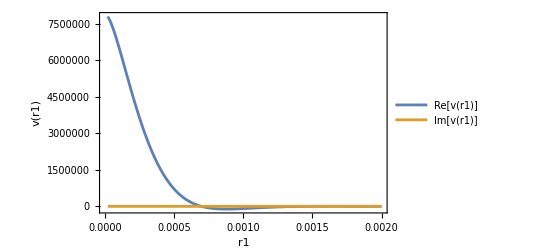

```mathematica
ListLinePlot[{Transpose[{r1,Re@result}],Transpose[{r1,Im@result}]},PlotLegends->{"Re[v(r1)]","Im[v(r1)]"},Frame->True,FrameLabel->{"r1","v(r1)"},PlotRange->All]
```

```mathematica
v
```

7.32666×10^164-4.24032×10^161 ⅈ

```mathematica
a = 0;
b = 2;
g =1;
poly=a x^5 + b x^3 + g x - 1;
f = 1/poly;
roots=x/. Solve[poly==0,x];
residues=Table[Residue[f,{x,z0}],{z0,roots}];

N[Total[residues*roots^2]]
```

0.5+0. ⅈ

```mathematica
InverseFourierTransform[Exp[-xi^2]/(Abs[xi] - rho),xi,t]
```

InverseFourierTransform[(ⅇ^(-xi^2))/(-rho+Abs[xi]),xi,t]